```mathematica
PositiveDefiniteMatrixQ[{{1/(x1^3 x2),-1/(x1^2 x2^2)},{-1/(x1^2 x2^2),1/(x1 x2^3)}}]
```

False

```mathematica
f[x1_,x2_]:=1/(1/x1+1/x2)
```

```mathematica
fh[x1_,x2_]:=1/f[x1,x2]
```

```mathematica
D[fh[x1,x2],{{x1,x2}}]
```

{-1/x1^2,-1/x2^2}

```mathematica
D[fh[x1,x2],{{x1,x2},2}]//TableForm
```

2/x1^3 | 0
0 | 2/x2^3

```mathematica
PositiveDefiniteMatrixQ[fh[x1,x2]*D[fh[x1,x2],{{x1,x2},2}]-D[fh[x1,x2],{{x1,x2}}]*D[fh[x1,x2],{{x1,x2}}]]
```

False

```mathematica
PositiveDefiniteMatrixQ[D[f[x1,x2],{{x1,x2}}]*D[f[x1,x2],{{x1,x2}}]-f[x1,x2]*D[f[x1,x2],{{x1,x2},2}]]
```

False

```mathematica
D[Log[f[x1,x2]],{{x1,x2}}]
```

{1/(x1^2 (1/x1+1/x2)),1/((1/x1+1/x2) x2^2)}

```mathematica
D[Log[f[x1,x2]],{{x1,x2},2}]//TableForm
```

1/(x1^4 (1/x1+1/x2)^2)-2/(x1^3 (1/x1+1/x2)) | 1/(x1^2 (1/x1+1/x2)^2 x2^2)
1/(x1^2 (1/x1+1/x2)^2 x2^2) | 1/((1/x1+1/x2)^2 x2^4)-2/((1/x1+1/x2) x2^3)

```mathematica
Eigenvalues[D[Log[f[x1,x2]],{{x1,x2},2}]]/.{x2-> x1}
```

{(-6 x1^4-2 √(x1^8))/(8 x1^6),(-6 x1^4+2 √(x1^8))/(8 x1^6)}

```mathematica
Manipulate[N[{(-6 x1^4-2 √(x1^8))/(8 x1^6),(-6 x1^4+2 √(x1^8))/(8 x1^6)}],{x1,0,100}]
```

```mathematica
b=x1^4+2 x1^3 x2+2 x1 x2^3+x2^4
a=x1^2 x2^2 (x1+x2)^2
c=(2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5)/x1^2 x2^2 (x1+x2)^2
```

x1^4+2 x1^3 x2+2 x1 x2^3+x2^4

x1^2 x2^2 (x1+x2)^2

(x2^2 (x1+x2)^2 (2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5))/x1^2

```mathematica
Reduce[{b≤ 0,a≥0,c≥ 0},{x1,x2}]
```

x1∈Reals&&x2==-x1

```mathematica
Reduce[(x1^4+2 x1^3 x2+2 x1 x2^3+x2^4)^2-4 (2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5)>=0,x1]
```

(x2|x1)∈Reals

```mathematica
x
```

```mathematica
Manipulate[Evaluate[Eigenvalues[D[Log[f[x1,x2]],{{x1,x2},2}]]],{x1,0,10},{x2,0,10}]
```

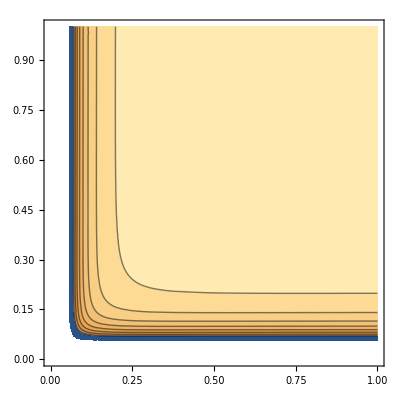

```mathematica
ContourPlot[Evaluate[Total[Eigenvalues[D[Log[f[x1,x2]],{{x1,x2},2}]]]],{x1,0,1},{x2,0,1}]
```

```mathematica
Plot3D[Evaluate[Eigenvalues[D[Log[f[x1,x2]],{{x1,x2},2}]]],{x1,-10,10},{x2,-10,10},PlotRange->All];
```

```mathematica
PositiveSemidefiniteMatrixQ[
Log[fh[x1,x2]]D[Log[fh[x1,x2]],{{x1,x2},2}]-D[Log[fh[x1,x2]],{{x1,x2}}]*D[Log[fh[x1,x2]],{{x1,x2}}]]//Simplify//TableForm
```

False

```mathematica
Solve[{f[θ x1 + (1-θ) y1,θ x2 + (1-θ )y2]≤f[x1,x2]^θ f[y1,y2]^(1-θ),0≤θ≤ 1},{x1,y1}]
```

$Aborted

```mathematica
Solve[Simplify[{y1,y2}.D[Log[f[x1,x2]],{{x1,x2},2}].{y1,y2}]==0,{y1}]
```

{{y1→(x1^2 x2^2 y2-√2 √(-x1^5 x2^3 y2^2-2 x1^4 x2^4 y2^2-x1^3 x2^5 y2^2))/(2 x1 x2^3+x2^4)},{y1→(x1^2 x2^2 y2+√2 √(-x1^5 x2^3 y2^2-2 x1^4 x2^4 y2^2-x1^3 x2^5 y2^2))/(2 x1 x2^3+x2^4)}}

```mathematica
{{a,b},{c,d}}.{x,y}//TableForm
```

a x+b y
c x+d y

```mathematica
PositiveSemidefiniteMatrixQ[
Log[fh[x1,x2]].D[Log[fh[x1,x2]],{{x1,x2},2}]-D[Log[fh[x1,x2]],{{x1,x2}}].D[Log[fh[x1,x2]],{{x1,x2}}]]
```

False

```mathematica
Log[fh[x1,x2]]*D[Log[fh[x1,x2]],{{x1,x2},2}]-D[Log[fh[x1,x2]],{{x1,x2}}]*D[Log[fh[x1,x2]],{{x1,x2}}]//TableForm
```

-1/(x1^4 (1/x1+1/x2)^2)+(-1/(x1^4 (1/x1+1/x2)^2)+2/(x1^3 (1/x1+1/x2))) Log[1/x1+1/x2] | -1/(x1^4 (1/x1+1/x2)^2)-Log[1/x1+1/x2]/(x1^2 (1/x1+1/x2)^2 x2^2)
-1/((1/x1+1/x2)^2 x2^4)-Log[1/x1+1/x2]/(x1^2 (1/x1+1/x2)^2 x2^2) | -1/((1/x1+1/x2)^2 x2^4)+(-1/((1/x1+1/x2)^2 x2^4)+2/((1/x1+1/x2) x2^3)) Log[1/x1+1/x2]

```mathematica
Log[fh[x1,x2]]
```

Log[1/x1+1/x2]

```mathematica
Solve[Evaluate[Eigenvalues[{{1/(x1+x2)^2-1/x1^2,1/(x1+x2)^2},{1/(x1+x2)^2,1/(x1+x2)^2-1/x2^2}}]]==0,{x1,x2}]
```

{}

```mathematica
Evaluate[Eigenvalues[{{1/(x1+x2)^2-1/x1^2,1/(x1+x2)^2},{1/(x1+x2)^2,1/(x1+x2)^2-1/x2^2}}]]
```

{(-x1^4-2 x1^3 x2-2 x1 x2^3-x2^4-√((x1^4+2 x1^3 x2+2 x1 x2^3+x2^4)^2-4 (2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5)))/(2 x1^2 x2^2 (x1+x2)^2),(-x1^4-2 x1^3 x2-2 x1 x2^3-x2^4+√((x1^4+2 x1^3 x2+2 x1 x2^3+x2^4)^2-4 (2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5)))/(2 x1^2 x2^2 (x1+x2)^2)}

```mathematica
Reduce[{(-x1^4-2 x1^3 x2-2 x1 x2^3-x2^4-√((x1^4+2 x1^3 x2+2 x1 x2^3+x2^4)^2-4 (2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5)))/(2 x1^2 x2^2 (x1+x2)^2)==0,(-x1^4-2 x1^3 x2-2 x1 x2^3-x2^4+√((x1^4+2 x1^3 x2+2 x1 x2^3+x2^4)^2-4 (2 x1^5 x2^3+4 x1^4 x2^4+2 x1^3 x2^5)))/(2 x1^2 x2^2 (x1+x2)^2)==0},{x1,x2}]
```

False

```mathematica
Clear[x1,x2]
PositiveSemidefiniteMatrixQ[-{{1/(x1+x2)^2-1/x1^2,1/(x1+x2)^2},{1/(x1+x2)^2,1/(x1+x2)^2-1/x2^2}}]
```

False

```mathematica
PositiveSemidefiniteMatrixQ[{{1,0},{0,2}}]
```

True

```mathematica
Manipulate[Plot3D[{m1,m2}.{{1/(x1+x2)^2-1/x1^2,1/(x1+x2)^2},{1/(x1+x2)^2,1/(x1+x2)^2-1/x2^2}}.{m1,m2},{m1,-10,10},{m2,-10,10}],{x1,-100,100},{x2,-100,100}]
```

```mathematica
Manipulate[Plot3D[{m1,m2}.{{1/(x1+x2)^2-1/x1^2,1/(x1+x2)^2},{1/(x1+x2)^2,1/(x1+x2)^2-1/x2^2}}.{m1,m2},{m1,-10,10},{m2,-10,10}],{x1,-100,100},{x2,-100,100}]
```

```mathematica
Plot3D[1/(1/x1+1/x2),{x1,-10,0},{x2,-10,0},PlotRange->All]
```

-Graphics3D-

```mathematica
Expand[(1+x)^(1/2)]
```

√(1+x)

```mathematica
Manipulate[{1+Exp[θ x]Exp[(1-θ)y],(1+Exp[x])^θ(1+Exp[y])^(1-θ)},{θ,0,1},{x,0,1},{y,0,1}]
```

```mathematica
Log[1]
```

0

```mathematica
Simplify[Log[Exp[2]]]
```

2